```mathematica
(1 Problem)
```

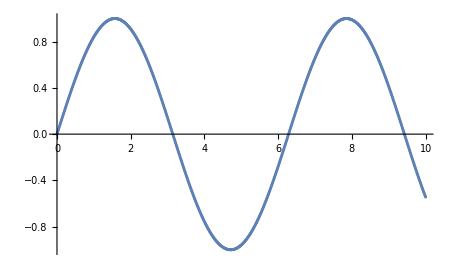

```mathematica
α = 1;
k= 1;
dt = 0.01;
t= Range[0,10,dt];
ω = t*0;θ= t*0;
ω[[1]]=1;θ[[1]]=0;
Do[
ω[[i+1]]= ω[[i]]-k θ[[i]]^α  dt;
θ[[i+1]]= θ[[i]] +ω[[i+1]] dt;
,{i,1,Length[t]-1}]
pList = Table[{t[[i]],θ[[i]]},{i,Length[t]}];
ListPlot[pList]
```

```mathematica
Tperiod[pdata_]:=(f=Abs[Fourier[pdata]];
peaksize=Last[TakeLargest[f,2]];
peaks=Flatten[Position[f,x_/;x>=peaksize]];
pos=First[peaks]; n=Length@pdata ;
fr=Abs[Fourier[pdata Exp[2 Pi I (pos-2) N[Range[0,n-1]]/n],FourierParameters->{0,2/n}]];
frpos=Position[fr,Max[fr]][[1,1]];
N[n/(pos-2+2 (frpos-1)/n)]*dt);(*creat a function to take the solution and find the period using fourier analysis*)
```

```mathematica
(*for checking period independance as the initial velocity is proportional to the amplitude.*)
```

```mathematica
Do[ α = 1;
k= 1;
dt = 0.01;
t= Range[0,10,dt];
ω = t*0;θ= t*0;
ω[[1]]=ω1;θ[[1]]=0;
Do[
ω[[i+1]]= ω[[i]]-k θ[[i]]^α  dt;
θ[[i+1]]= θ[[i]] +ω[[i+1]] dt;
,{i,1,Length[t]-1}];
Print[Tperiod[θ]],{ω1,.2,1,.2}]
```

6.58778

6.58778

6.58778

«2 more identical outputs»

```mathematica
(Anharmonic For)
```

```mathematica
Do[ α = 3;
k= 1;
dt = 0.01;
t= Range[0,10,dt];
ω = t*0;θ= t*0;
ω[[1]]=ω1;θ[[1]]=0;
Do[
ω[[i+1]]= ω[[i]]-k θ[[i]]^α  dt;
θ[[i+1]]= θ[[i]] +ω[[i+1]] dt;
,{i,1,Length[t]-1}]; 
pd=θ;
Print[Tperiod[pd]],{ω1,.2,1,.2}]
```

13.8781

11.6512

8.04174

7.4003

6.48544

```mathematica
amplitude dependent is of period
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
2 problem
```

```mathematica
q=1/2; hold={};
g= 9.8;l=9.8;
dt = 0.004;
Fd = 1.2;Ω =2/3;
t= Range[0,150,dt];
Do[ω1 = t*0;θ1= t*0;θ2= t*0;
ω1[[1]]=0;θ1[[1]]=0.2+va;
Do[
ω1[[i+1]]= ω1[[i]]-((g/l)Sin[θ1[[i]]] +q ω1[[i]]-Fd Sin[ Ω t[[i]]])*dt ;
θ1[[i+1]]= θ1[[i]] +ω1[[i+1]] dt;
,{i,1,Length[t]-1}]
ω2 = t*0;θ2[[1]]=0.2+.001+va;
Do[
ω2[[i+1]]= ω2[[i]]-((g/l)Sin[θ2[[i]]] +q ω2[[i]]-Fd Sin[ Ω t[[i]]])*dt ;
θ2[[i+1]]= θ2[[i]] +ω2[[i+1]] dt;
,{i,1,Length[t]-1}];
hold=Append[hold,Abs[θ1-θ2]];
pList = Table[{t[[i]],Abs[θ1[[i]]-θ2[[i]]]},{i,Length[t]-4}];,{va,0,4,.2}]
```

-5.02466+0.229204 p

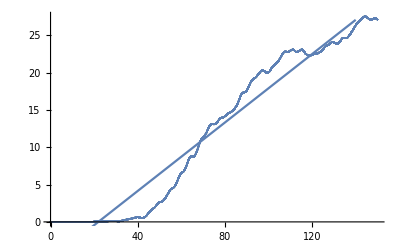

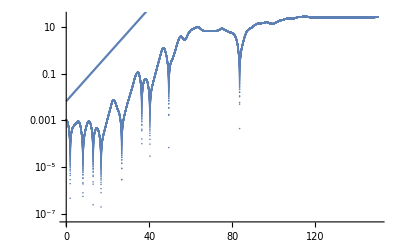

```mathematica
sum=Sum[hold[[i]],{i,1,Length[hold]}]/Length[hold];
data = Table[{t[[i]],sum[[i]]},{i,Length[t]-4}];
line=Fit[data,{1,p},p]
Show[{ListPlot[data],Plot[-5.024663768476222+0.22920435283192092 p,{p,0,140}]}]
fig=Table[{t[[i]],hold[[1]][[i]]},{i,Length[t]-4}];(*for particular intail values*)
Show[{ListLogPlot[fig],Plot[-5.024663768476222+0.22920435283192092 p,{p,0,140}]}](*for specific intial conditions*)
```

```mathematica
D[-5.024663768476222+0.22920435283192092 p,p](* for exponent*)
```

0.229204

```mathematica
3 problem
```

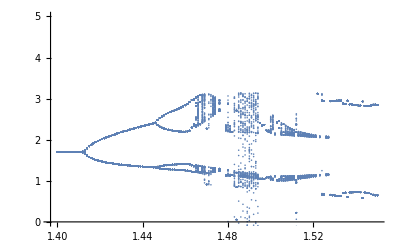

```mathematica
q=1/2;g= 9.8;l=9.8;Ω =2/3;dt = 2 π/Ω 0.01;t= Range[0,300*(2π)/Ω,dt];
diag = {};
FD = Range[1.3,1.55,0.001];
Do[
ω1 = t*0;θ1= t*0;θ2= t*0;
ω1[[1]]=0;θ1[[1]]=0.2;
Do[(*solving for the EOM of θ *)
ω1[[i+1]]= ω1[[i]]-((g/l)Sin[θ1[[i]]] +q ω1[[i]]-FD[[j]] Sin[ Ω t[[i]]])*dt ;
θ1[[i+1]]= θ1[[i]] +ω1[[i+1]] dt;
If[θ1[[i+1]]<-π, θ1[[i+1]] +=2π];
If[θ1[[i+1]]>π, θ1[[i+1]] -=2π];
,{i,1,Length[t]-1}];
Do[(*finding the values of θ to be ploted on the diag*)
diag= Append[diag,{FD[[j]],θ1[[i]]} ]
,{i,12000,Length[t],100}];
,{j,1,Length[FD]}]
ListPlot[diag,PlotRange->5]
```

```mathematica
FD = {1.4125,1.445,1.465}
```

```mathematica
δ = (1.445-1.4125)/(1.465-1.445)
```

```mathematica
problem 4
```

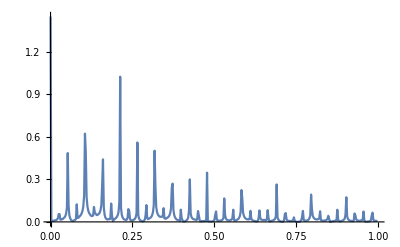

```mathematica
FD = 1.47; q=1/2; g= 9.8;l=9.8; Ω =2/3;
dt = 0.005;
t= Range[0,400,dt];
ω1 = t*0;θ1= t*0;
ω1[[1]]=0;θ1[[1]]=0.2;
Do[
ω1[[i+1]]= ω1[[i]]-((g/l)Sin[θ1[[i]]] +q ω1[[i]]-FD Sin[ Ω t[[i]]])*dt ;
θ1[[i+1]]= θ1[[i]] +ω1[[i+1]] dt;
If[θ1[[i+1]]<-π, θ1[[i+1]] +=2π];
If[θ1[[i+1]]>π, θ1[[i+1]] -=2π];
,{i,1,Length[t]-1}];
dftdata = Abs[Fourier[θ1,FourierParameters->{1,-1}]];
fData =  Table[{(i-1)/t[[-1]],2dftdata[[i]]/Length[t]},{i,Length[t]}];
ListPlot[fData[[1;;400]], PlotRange->All, Joined->True]
```

```mathematica
peaks = FindPeaks[dftdata];
fData[[peaks[[2]][[1]]]][[1]](*finding the first peak*)
```

0.025

```mathematica
5 Problem
```

```mathematica
dt = 0.0001;
t= Range[0,50,dt];σ = 10;r = Range[24,25,0.1];b = 8/3;
xintial = {1,1.00001}; 
car={};
Do[
x = t*0;y=t*0;z=t*0;
Do[
x[[1]] = xintial[[n]];y[[1]]=0;z[[1]]=0;
held = {z,z};
Do[
x[[i+1]]=x[[i]]+ σ (y[[i]]-x[[i]])*dt;
y[[i+1]] = y[[i]] + (-x[[i]] z[[i]]+r[[j]] x[[i]]-y[[i]])*dt;
z[[i+1]] = z[[i]] + (x[[i]] y[[i]]-b z[[i]])*dt; 
held[[n]][[i+1]]=z[[i+1]];
,{i,Length[t]-1}];
,{n,1,2}];
diff = Abs[held[[1]]-held[[2]]];
plist= Table[{t[[i]],diff[[i]]},{i,1,Length[t]}];
car=Append[car,plist];

,{j,Length[r]}]
expon=Table[line=Fit[car[[i]],{1,p},p];D[line,p],{i,1 , Length[car]}](* caluculating the exponent by fitting the data and taking the derrevitave to get the slop*)


(* we see that around 24.7 (elemnt number 8) the exponent gets larger than one significantly
0.12 , the other non negative slops are due to numericall inacurcies and can be neglected*)
```

{1.21325×10^-7,4.75641×10^-6,0.000816689,0.021004,0.0344034,0.0875752,0.0463546,0.122386,0.0803054,0.161004,0.103962}

```mathematica
(*method of problem 2 is computationally heavy so we used a simple version where we did not calcute for different intial conditions and take the averge to have a clear fitting data but we make the fit for just one intial condtion *)
```